# Lab 3 Appendix A: Max Distance

## Parameters

```mathematica
Remove["`*"]; (* Remove all global symbols *)
```

#### Physical Constants

```mathematica
g:={0,-9.81}; (* Acceleration of gravity, m/s^2 *)
```

```mathematica
γ:=1; (* Type of flow, 1 = laminar *)
```

```mathematica
ρ:=1.3; (* Fluid mass density, kg/m^3 *)
```

```mathematica
CD:=0.3; (* Drag coefficient *)
```

#### Object Properties

```mathematica
m:=0.045; (* Particle mass, kg *)
```

```mathematica
r:=0.02; (* Particle radius, m *)
```

#### Initial Conditions

```mathematica
t0=0; (* Initial time *)
```

```mathematica
tf=12; (* Final time *)
```

```mathematica
x0:={0,0}; (* Initial position, m *)
```

```mathematica
v0:=80; (* Initial velocity, m/s *)
```

## Forces and Energy

#### Total Force

```mathematica
F[x_?VectorQ,v_?VectorQ]:= m g- kD  Norm[v]^γ v/Norm[v];
```

where

```mathematica
kD:=1/2 CD ρ A; (* Viscous damping coefficient *)
```

```mathematica
A:=r^2 π; (* Cross section area, m^2 *)
```

#### Potential and Kinetic Energy

```mathematica
Ep[x_?VectorQ]:= -m g.x;
```

```mathematica
Ek[v_?VectorQ]:=(m v.v)/2;
```

## Equations of Motion

```mathematica
SolveODE[
t0_,tf_,
x0_?VectorQ,v0_?VectorQ,
method_:Automatic,h_:Automatic
]:=Module[ 
{X,V, sol},
sol=NDSolve[
{
(* Differential Equations: *)
	X'[t]==V[t],
	m V'[t]==F[ X[t],V[t] ],
(* Initial conditions: *)
	X[t0]==x0,
	V[t0]==v0
},
{X,V}, (* Dependent variables *)
{t,t0,tf} (* Range of the independent variable *)
,Method->method
,StartingStepSize->h
,MaxStepSize->h
,MaxSteps->Infinity
];
( {X,V}/.sol )[[1]]
];
```

## Solve Equations

Subroutine that solves ode using Runge-Kutta 4th order with h = 0.01 for a given angle

```mathematica
FindMax[θ_]:=Module[
{X,V,tmax},
{X,V}=SolveODE[t0,tf,x0,{v0 Cos[θ π/180],v0 Sin[θ π/180]},"ExplicitRungeKutta",0.01];
tmax=t/.FindRoot[X[t][[2]]==0,{t,10,tf}] ;
X[tmax][[1]]
];
```

Find max distance without viscous damping (reference solution)

```mathematica
CD=0.0;
MaxXref=Quiet[Table[{θ,FindMax[θ]},{θ,40,50,0.2}]];
```

Find max distance with viscous damping enabled, laminar flow

```mathematica
CD=0.3;γ:=1;
MaxXvisc=Quiet[Table[{θ,FindMax[θ]},{θ,40,50,0.2}]];
```

Find max distance with viscous damping enabled, turbulent flow

```mathematica
CD=0.3;γ:=2;
MaxXvisc2=Quiet[Table[{θ,FindMax[θ]},{θ,32,42,0.2}]];
```

## The Results

```mathematica
MaxX=Transpose[{
MaxXvisc[[All,1]],MaxXvisc[[All,2]],MaxXref[[All,2]],
Table["    ",{i,0,10,0.2}],
MaxXvisc2[[All,1]],MaxXvisc2[[All,2]]
}]//TableForm
```

40. | 618.821 | 642.484 |      | 32. | 210.29
40.2 | 619.473 | 643.259 |      | 32.2 | 210.457
40.4 | 620.094 | 644.003 |      | 32.4 | 210.616
40.6 | 620.685 | 644.716 |      | 32.6 | 210.767
40.8 | 621.246 | 645.397 |      | 32.8 | 210.911
41. | 621.777 | 646.046 |      | 33. | 211.047
41.2 | 622.278 | 646.665 |      | 33.2 | 211.176
41.4 | 622.748 | 647.251 |      | 33.4 | 211.297
41.6 | 623.189 | 647.806 |      | 33.6 | 211.41
41.8 | 623.599 | 648.33 |      | 33.8 | 211.517
42. | 623.979 | 648.822 |      | 34. | 211.616
42.2 | 624.328 | 649.282 |      | 34.2 | 211.707
42.4 | 624.648 | 649.711 |      | 34.4 | 211.792
42.6 | 624.937 | 650.107 |      | 34.6 | 211.869
42.8 | 625.196 | 650.473 |      | 34.8 | 211.938
43. | 625.425 | 650.806 |      | 35. | 212.001
43.2 | 625.623 | 651.108 |      | 35.2 | 212.056
43.4 | 625.791 | 651.378 |      | 35.4 | 212.104
43.6 | 625.929 | 651.617 |      | 35.6 | 212.145
43.8 | 626.037 | 651.823 |      | 35.8 | 212.179
44. | 626.114 | 651.998 |      | 36. | 212.206
44.2 | 626.162 | 652.141 |      | 36.2 | 212.225
44.4 | 626.179 | 652.252 |      | 36.4 | 212.238
44.6 | 626.165 | 652.332 |      | 36.6 | 212.243
44.8 | 626.122 | 652.38 |      | 36.8 | 212.241
45. | 626.048 | 652.396 |      | 37. | 212.233
45.2 | 625.945 | 652.38 |      | 37.2 | 212.217
45.4 | 625.811 | 652.332 |      | 37.4 | 212.195
45.6 | 625.647 | 652.252 |      | 37.6 | 212.165
45.8 | 625.452 | 652.141 |      | 37.8 | 212.129
46. | 625.228 | 651.998 |      | 38. | 212.085
46.2 | 624.973 | 651.823 |      | 38.2 | 212.035
46.4 | 624.689 | 651.617 |      | 38.4 | 211.978
46.6 | 624.374 | 651.378 |      | 38.6 | 211.914
46.8 | 624.03 | 651.108 |      | 38.8 | 211.844
47. | 623.655 | 650.806 |      | 39. | 211.766
47.2 | 623.251 | 650.473 |      | 39.2 | 211.682
47.4 | 622.816 | 650.107 |      | 39.4 | 211.591
47.6 | 622.352 | 649.711 |      | 39.6 | 211.493
47.8 | 621.857 | 649.282 |      | 39.8 | 211.388
48. | 621.333 | 648.822 |      | 40. | 211.277
48.2 | 620.779 | 648.33 |      | 40.2 | 211.159
48.4 | 620.195 | 647.806 |      | 40.4 | 211.035
48.6 | 619.582 | 647.251 |      | 40.6 | 210.903
48.8 | 618.939 | 646.665 |      | 40.8 | 210.765
49. | 618.266 | 646.046 |      | 41. | 210.621
49.2 | 617.563 | 645.397 |      | 41.2 | 210.47
49.4 | 616.831 | 644.716 |      | 41.4 | 210.312
49.6 | 616.069 | 644.003 |      | 41.6 | 210.147
49.8 | 615.278 | 643.259 |      | 41.8 | 209.976
50. | 614.458 | 642.484 |      | 42. | 209.799

Maximimum length (in meters) as a function of initial velocity angle (in degrees):

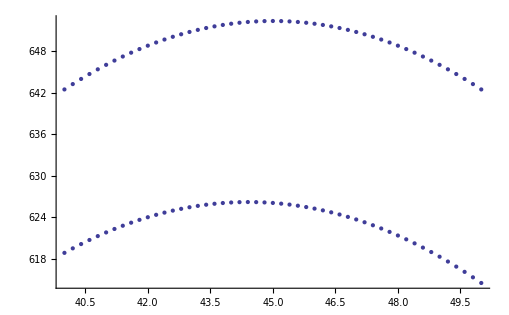

```mathematica
Show[ListPlot[Table[ MaxXref[[i,All]],{i,1,51}]],
ListPlot[Table[ MaxXvisc[[i,All]],{i,1,51}]]]
```

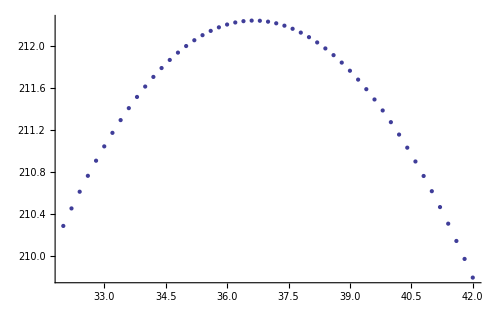

```mathematica
ListPlot[Table[MaxXvisc2[[i,All]],{i,1,51}]]
```

Reference solution without viscous forces:

```mathematica
Max[MaxXref[[All,2]]]
```

652.396

```mathematica
MaxXref[[Position[ MaxXref[[All,2]],Max[MaxXref[[All,2]]]][[1]][[1]],1]]
```

45.

With viscous damping, laminar flow:

```mathematica
Max[MaxXvisc[[All,2]]]
```

626.179

```mathematica
MaxXvisc[[Position[ MaxXvisc[[All,2]],Max[MaxXvisc[[All,2]]]][[1]][[1]],1]]
```

44.4

With viscous damping, turbulent flow:

```mathematica
Max[MaxXvisc2[[All,2]]]
```

212.243

```mathematica
MaxXvisc2[[Position[ MaxXvisc2[[All,2]],Max[MaxXvisc2[[All,2]]]][[1]][[1]],1]]
```

36.6